# Cytotoxicity

This program is designed to perform calculations and determine the IC50 value based on raw data from a cytotoxicity assay using a 96 - well plate.  To begin, fill out the information in the text boxes provided.  This information will be used to customize an Excel template for you to fill out and to get the best logistic fit for your data.  Click “OK” when you are done.

```mathematica
Grid[{{"List the concentrations, including 0, separated by commas (ex. 100,75,50,25,15,0):",InputField[Dynamic[conc],String]},{"What is the unit of concentration? (ex. ug/uL)",InputField[Dynamic[concUnit],String]},{"Enter an estimate for the IC50 value (ex. 700):",InputField[Dynamic[IC50est],Number]}},ItemSize->Full,Alignment->{{Right,Left},{Bottom,Top}}]
SelectionMove[EvaluationNotebook[],Next,Cell,2]
```

List the concentrations, including 0, separated by commas (ex. 100,75,50,25,15,0): | 
What is the unit of concentration? (ex. ug/uL) | 
Enter an estimate for the IC50 value (ex. 700): |

```mathematica
Button["OK",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

OK

Click “Next” below.

```mathematica
concs=Read[StringToStream[#],Number]&/@StringSplit[conc,","];
numConc=Length[concs];
rowLabel=Insert[concs,"background",-1];
Button["Next",SelectionEvaluate[SelectedNotebook[]]]
```

Next

After you' ve entered information about your assay, click the "Download Template" button to save the customized template Excel file with the extension ".xlsx" to your computer.  Open the downloaded file.  The first column will contain the concentrations you entered above and a row labeled background for the background readings.  Fill in the intensity readings (1 per cell) in the corresponding rows.  See the example below for help.  Remember to save your changes when you are done entering data!

```mathematica
Button["Download Template",Export[SystemDialogInput["FileSave"],rowLabel,"XLSX"],Method->"Queued"]
```

Download Template

-Graphics-

After you have updated and saved the Excel file, you are ready to upload your data.  Click the “Upload File” button and select the completed Excel file.

```mathematica
Button["Upload File",file=SystemDialogInput["FileOpen"];
If[file≠"$Canceled",data=Import[file,"Data"][[1]];],Method->"Queued"] (*code was adapted from Vahagn Poghosyan's reply in the StackExchange forum:
https://mathematica.stackexchange.com/questions/19985/system-dialog-input-with-button *)
```

Upload File

The program now has all the information it needs! Click "Get Results!" to display a visual representation of your well plate,  a plot with error bars, the best fit 4-parameter logistic curve, the IC50 value, and the equation of the logistic (dose-response) curve.  Click the “Save” button below any figure you want to save to your computer.

```mathematica
Button["Get Results!",FrontEndExecute[FrontEndToken["EvaluateNotebook"]]]
```

Get Results!

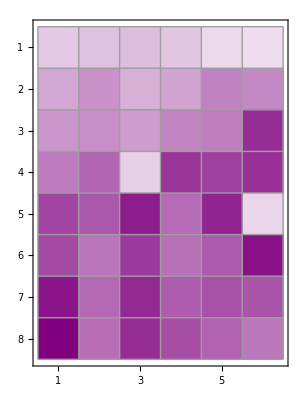

Save

```mathematica
bkgdPos=Flatten[Position[rowLabel,"background"]];
datapts=data[[1;;numConc,2;;All]];
bkgd=Flatten[data[[bkgdPos,2;;All]]];
bkgd=DeleteCases[bkgd,""];
bkgdAvg=Mean[bkgd];
correctedData=datapts-bkgdAvg;
controlPos=Flatten[Position[rowLabel,0]];
control=Flatten[datapts[[controlPos,All]]];
controlAvg=Mean[control];
viability=correctedData/controlAvg*100;
graphic=MatrixPlot[viability,ColorFunction->(Blend[{White,LightPurple,Purple},#1]&),Mesh->All]
Button["Save",Export[SystemDialogInput["FileSave"],graphic,"PDF"],Method->"Queued"]
```

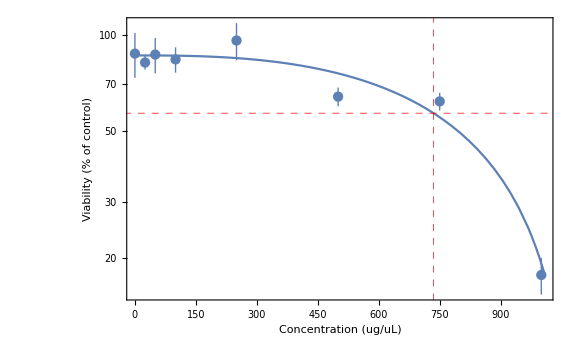

Save

The IC50 value is 734.942

The equation of the dose-response (4P logistic) curve is (3.56692×10^7)/(1.73727×10^-14 x^2.678+1)-3.56691×10^7

```mathematica
numRows=Range[1,numConc];
cleanData=Function[n,row=viability[[n]];
med=Median[row];
upper=med*1.28;
lower=med*0.86;
findOutliers=(If[#1<lower||#1>upper,out,{#1}]&)/@row;
noOutliers=DeleteCases[findOutliers,out];noOutliers=Flatten[noOutliers]];
newViability=Map[cleanData,numRows];
avgFunc=Function[x,Mean[newViability[[x]]]];
avgWithErrorFunc=Function[x,Around[newViability[[x]]]];
viabilityAvg=Map[avgFunc,numRows];
viabilityAvgWithError=Map[avgWithErrorFunc,numRows];
dataPlotError=Transpose[{concs,viabilityAvgWithError}];
dataPlotPts=Transpose[{concs,viabilityAvg}];
Clear[x];
model=(a1-a2)/(1+If[x==0,0,(x/x0)^h])+a2;
modelDisp=(a1-a2)/(1+(x/x0)^h)+a2;
nlm=Quiet[NonlinearModelFit[dataPlotPts,model,{{a1,100},{a2,0},{x0,IC50est},{h,2}},x,MaxIterations->1000]]; (*code adapted from JimB's reply in the StackExchange forum:
https://mathematica.stackexchange.com/questions/238057/find-fit-error-4p-logistic *)
coef=nlm["BestFitParameters"];
curvefit=model/.coef;
curvefitDisp=modelDisp/.coef;
vmax=Max[viabilityAvg];
vmin=Min[viabilityAvg];
yval=vmax-.5*(vmax-vmin);
IC50=Quiet[Solve[curvefit==yval,x,Reals]];
IC50=Flatten[IC50];
IC50=x/.IC50;
xmin=Quiet[Solve[curvefit==vmin,x,Reals]];
xmin=Flatten[xmin];
Clear[x];
xminEnd=x/.xmin;
plotcurve=LogPlot[curvefit,{x,0,xminEnd},GridLines->{{IC50},{yval}},GridLinesStyle->Directive[Red, Dashed]];
errorbars=ListLogPlot[dataPlotError];
xLabel=StringForm["Concentration (``)",concUnit];
graphic2=Show[plotcurve,errorbars,Axes->False, ImageSize->Large,LabelStyle->Directive[Bold, Medium],Frame->True,FrameLabel->{xLabel,"Viability (% of control)"},PlotRange->All]
Button["Save",Export[SystemDialogInput["FileSave"],graphic2,"PDF"],Method->"Queued"]
myPrint[args__,{style__}]:=Print[Row[{args},BaseStyle->{style}]] (*code adapted from Kuba's reply in the StackExchange forum:
https://mathematica.stackexchange.com/questions/104817/styles-and-print-and-output *)
text1=myPrint["The IC50 value is ",IC50,{FontSize->14,FontWeight->Bold,Background->LightBlue}]
text2=myPrint["The equation of the dose-response (4P logistic) curve is ",curvefitDisp,{FontSize->14,FontWeight->Bold,Background->LightBlue}]
```

```mathematica
Module[{nb},nb=EvaluationNotebook[];
NotebookFind[EvaluationNotebook[],"Input",All,CellStyle];
SetOptions[NotebookSelection[nb],CellOpen->False,ShowCellBracket->True]]
(*code adapted from David Reiss's response in Google group:
https://groups.google.com/g/comp.soft-sys.math.mathematica/c/OxD-QT-YsHw?pli=1 *)
```